# D3-branes in Pilch Warner background

```mathematica
AppendTo[$Path,ToFileName[{NotebookDirectory[]}]<>"Packages"];
<<Dbrane.m
<<PilchWarner.m
```

## Target space metric and C_4

### Targe space metric, initialization cell

```mathematica
(*work on the c convention*)
PWc 
(*We work in the string frame*)
vielbTarget=c^(-1/4) DiagonalMatrix[{vx[c,θ],vx[c,θ],vx[c,θ]ρ,vx[c,θ]ρ Sin[ω],vrc[c,θ]}]/.θ->π/2/.vRule/.X1X2Rule//PowerExpand//Simplify
coordinates={x,ρ,ω,η,c};
Clear[θ]
```

{{1/(√((-1+c^2)/A[c])),0,0,0,0},{0,1/(√((-1+c^2)/A[c])),0,0,0},{0,0,ρ √(A[c]/(-1+c^2)),0,0},{0,0,0,ρ √(A[c]/(-1+c^2)) Sin[ω],0},{0,0,0,0,1/((-1+c^2) √A[c])}}

### The target space metric, text

The deformed AdS5 only:

vx[c,θ]^2(dx_(||))^2=vx[c,θ]^2(dx^2+dρ^2+ρ^2 dΩ_2^2)
	dΩ_2^2=dω^2+Sin[ω]^2 dη^2

The string frame G_MN and the Einstein frame g_MN are related by a general conformal transformation:

g_MN=ⅇ^(-(4Φ)/(D-2))G_MN=ⅇ^(-Φ/2)G_MN

We will work in the string frame. At θ=π/2, it is Exp[Φ/2]=1/√c:

```mathematica
√expDilaton[c,θ,0]//.formsRules/.X1X2Rule//PowerExpand//Simplify
```

1/(√c)

### C_4=(c A[c]^2)/((-1+c^2)^2)ρ^2 Sin[ω]dx⋀dρ⋀dω⋀dη

WZ term has an analogous structure as the kappa projector for D-branes. Its only contribution comes from C_(4).
We use:  dC_4=4 F_5

```mathematica
dC4=4 F5RR[1,2,3,4,5]/.F5Rules[[1]]/.cRule//.formsRules/.X1X2Rule/.ARule/.θ->π/2//PowerExpand//Simplify
```

(A[c] (-4 c+(-1+c^2) A[c]))/((-1+c^2)^3)

F_5=(A[c] (-4 c+(-1+c^2) A[c]))/((-1+c^2)^3)dx1⋀dx2⋀dx3⋀dx4⋀dc
      =(A[c] (-4 c+(-1+c^2) A[c]))/((-1+c^2)^3)ρ^2 Sin[ω]dx⋀dρ⋀dω⋀dη⋀dc

```mathematica
Integrate[dC4/.explicitARule,c]//Simplify;
%/.Log[(c-1)/(c+1)]-> 2/(c^2-1)(A[c]-c)/.Log[1+c]->Log[1-c]- 2/(c^2-1)(A[c]-c)//Simplify(*An imaginary ⅈ π from log[1-c] to log[c-1] is ignored*)
```

(c A[c]^2)/((-1+c^2)^2)

C_4=(c A[c]^2)/((-1+c^2)^2)ρ^2 Sin[ω]dx⋀dρ⋀dω⋀dη

## D3-brane

We will work in Minkowski signature and mostly minus, unless otherwise stated.

### D3-brane worldvolume: ρ[c] parametrization

```mathematica
pullback={x,ρ[c],ω,η,c};
inducedCoord={x,ω,η,c};
metricWEucl=induced[metric[0][vielbTarget],coordinates,inducedCoord,pullback];
metricWMink=DiagonalMatrix@Join[{1},-{1,1,1}].metricWEucl
```

{{A[c]/(-1+c^2),0,0,0},{0,-(A[c] ρ[c]^2)/(-1+c^2),0,0},{0,0,-(A[c] Sin[ω]^2 ρ[c]^2)/(-1+c^2),0},{0,0,0,-1/((-1+c^2)^2 A[c])-(A[c] ρ'[c]^2)/(-1+c^2)}}

### Collection of some results: LDBIeucl, LDBImink, LWZ, ρSolution, dρSolution

```mathematica
(* Note that I define LDBI without the e^-Φ prefactor *)
$Assumptions=c>1&&κ>1&&A[c]>1;
LDBIeucl=√Det[metricWEucl+({{0, 0, 0, f}, {0, 0, 0, 0}, {0, 0, 0, 0}, {-f, 0, 0, 0}})]//PowerExpand//Simplify ;
LDBImink=√(-Det[metricWMink+({{0, 0, 0, f}, {0, 0, 0, 0}, {0, 0, 0, 0}, {-f, 0, 0, 0}})])//Simplify;
LWZ=-Sin[ω](c A[c]^2)/((-1+c^2)^2)ρ[c]^2 ρ'[c]; (*LWZ=(A[c] (-4 c+(-1+c^2) A[c]))/((-1+c^2)^3)ρ^3/3 Sin[ω] ;*)
ρSolution={ρ->Function[{c},(√(-1+c^2) κ)/(1-√(-1+c^2) C[1])]};
dρSolution={ρ'[c_]:> c/((c^2-1)^(3/2))ρ[c]^2/κ};
```

### D3-brane projector and the susy condition

#### Construct the projector

```mathematica
dBraneProj[inducedCoord][{f},{{1,4}}]
projector=-%/LDBI/.γ-> γComponentsLocal[vielbTarget,coordinates,inducedCoord,pullback]/.Γ->antisym[Γ]//Simplify;
%/.toSubscriptRule[Γ]
```

f 𝒦 γ[2,3]+γ[1,2,3,4]

-(A[c] Sin[ω] ρ[c]^2 ((-1+c^2)^2 f 𝒦 Γ_{3,4}+√(-1+c^2) Γ_{1,3,4,5}+(-1+c^2) A[c] Γ_{1,2,3,4} ρ'[c]))/((-1+c^2)^3 LDBI)

#### Simplify the projector

```mathematica
e1=Coefficient[projector,Γ[1,2,3,4]];

e2=Collect[projector/e1,basis[Γ][projector],PowerExpand//Simplify];
e21=Γ[1,2,3,4];

-ncContract[Γ][e21,e2]/.Γ->gammaContract[1]/.gammaContract[1]-> Γ ;
e22=Collect[%,basis[Γ][%],Simplify];
{e1,{e21,e22}}

rest=Rest@e22;
-ncContract[Γ][Γ[2,5],rest]/.Γ->gammaContract[1]/.gammaContract[1]-> antisym[Γ];
{r1,r2}={Γ[2,5] First@% ,%/(First@%)}//Simplify
```

{-(A[c]^2 Sin[ω] ρ[c]^2 ρ'[c])/((-1+c^2)^2 LDBI),{Γ[1,2,3,4],1+((-1+c^2) f 𝒦 Γ[1,2])/(A[c] ρ'[c])-Γ[2,5]/(√(-1+c^2) A[c] ρ'[c])}}

{-Γ[2,5]/(√(-1+c^2) A[c] ρ'[c]),1+(-1+c^2)^(3/2) f 𝒦 Γ[1,5]}

The curly parenthesis mean Times.

#### Susy condition

```mathematica
e1/.LDBI-> LDBImink//PowerExpand//Simplify
Print[Style["The susy condition imposes that:",Red]]
Solve[%%==1,f]//Simplify
```

-(A[c] ρ'[c])/(√((1-(-1+c^2)^3 f^2+(-1+c^2) A[c]^2 ρ'[c]^2)/(-1+c^2)))

The susy condition imposes that:

{{f→-1/((-1+c^2)^(3/2))},{f→1/((-1+c^2)^(3/2))}}

### D3-brane action and eoms

#### Lagragian density (integrated out the 2-sphere)

```mathematica
Print[Style["Integrate out the 2-sphere and factor out the numeric constants, the Lagragian density is: ",Red]]
LDBIint=π/2 Integrate[1/π(c LDBImink),{ω,0,π}];
LWZint=π/2 Integrate[1/π LWZ,{ω,0,π}];
Ltotal=LDBIint+LWZint-κ f
```

Integrate out the 2-sphere and factor out the numeric constants, the Lagragian density is:

-f κ-(c A[c]^2 ρ[c]^2 ρ'[c])/((-1+c^2)^2)+(c A[c] √(ρ[c]^4 (1-(-1+c^2)^3 f^2+(-1+c^2) A[c]^2 ρ'[c]^2)))/((-1+c^2)^(5/2))

#### Equation of motion for f

```mathematica
Print[Style["EOM for f ",Red]]
eqf=D[LDBIint,f]==κ
fRule=Solve[eqf,f][[1]]//Simplify; (*Only one of the solutions satisfies the eom for f*)

Print[Style["The correct solution satisfies the eom for f, and it is:",Red]]
Assuming[c>1,eqf/.fRule//PowerExpand//Simplify//PowerExpand//Simplify]
fRule
```

EOM for f

-(c √(-1+c^2) f A[c] ρ[c]^4)/(√(ρ[c]^4 (1-(-1+c^2)^3 f^2+(-1+c^2) A[c]^2 ρ'[c]^2)))==κ

The correct solution satisfies the eom for f, and it is:

True

{f→-(κ √(1+(-1+c^2) A[c]^2 ρ'[c]^2))/(√((-1+c^2) ((-1+c^2)^2 κ^2+c^2 A[c]^2 ρ[c]^4)))}

#### Solutions: f and ρ[c]

The susy condition, combined with the eom for f gives the solution for f:

```mathematica
f==-(-1+c^2)^(-3/2)/.fRule;
Solve[%,ρ'[c]] //Simplify//PowerExpand//Simplify
```

{{ρ'[c]→-(c ρ[c]^2)/((-1+c^2)^(3/2) κ)},{ρ'[c]→(c ρ[c]^2)/((-1+c^2)^(3/2) κ)}}

Only one of them is the correct solution for the equation of motion for ρ, and it’s saved as dρSolution:

```mathematica
dρSolution
```

{ρ'[c_]:>(c ρ[c]^2)/((c^2-1)^(3/2) κ)}

```mathematica
LnoF=Assuming[c>1,Ltotal/.fRule//PowerExpand//Simplify];
$Assumptions=κ>0 &&ρ>0&&c[ρ]>1;
D[LnoF,ρ[c]]-D[D[LnoF,ρ'[c]],c]/.ARule//PowerExpand//Simplify;
%/.ρ''[c]->D[ρ'[c]/.dρSolution ,c]/.dρSolution//PowerExpand//Simplify//PowerExpand//Simplify
```

0

```mathematica
DSolve[ρ'[c]== (c ρ[c]^2)/((c^2-1)^(3/2) κ),ρ,c]
```

{{ρ→Function[{c},(√(-1+c^2) κ)/(1-√(-1+c^2) κ C[1])]}}

#### Action at the solution

```mathematica
Lsol=Ltotal/.fRule/.dρSolution//PowerExpand//Simplify//PowerExpand//Simplify
```

κ/((-1+c^2)^(3/2))

This is simply the Lagrange multiplier term, since the LDBI and LWZ cancel each other:

```mathematica
LDBIint+LWZint;
%/.fRule/.dρSolution//Simplify//PowerExpand
```

0

```mathematica
action=Assuming[ϵ>0,Integrate[Lsol,{c,1+ϵ^2/2,∞}]]
Series[%,{ϵ,0,0}]
```

(-1+(2+ϵ^2)/(ϵ √(4+ϵ^2))) κ

κ/ϵ-κ+O[ϵ]^1

#### Euclidean signature: eom for f

```mathematica
Print[Style["Integrate out the 2-sphere of ⅇ^-Φ LDBI and factor out the numeric constants: ",Red]]
LDBIint=π/2 Integrate[1/π c LDBIeucl,{ω,0,π}] 

Print[Style["EOM for f ",Red]]
eqf=D[LDBIint,f]==ⅈ κ
fRule=Solve[eqf,f][[2]]//Simplify; (*Only one of the solutions satisfies the eom for f*)

Print[Style["The correct solution satisfies the eom for f, and it is:",Red]]
Assuming[c>1,eqf/.fRule//PowerExpand//Simplify//PowerExpand//Simplify]
fRule
```

Integrate out the 2-sphere of ⅇ^-Φ LDBI and factor out the numeric constants:

(c A[c] ρ[c]^2 √(1+(-1+c^2)^3 f^2+(-1+c^2) A[c]^2 ρ'[c]^2))/((-1+c^2)^(5/2))

EOM for f

(c √(-1+c^2) f A[c] ρ[c]^2)/(√(1+(-1+c^2)^3 f^2+(-1+c^2) A[c]^2 ρ'[c]^2))==ⅈ κ

The correct solution satisfies the eom for f, and it is:

True

{f→(ⅈ κ √(1+(-1+c^2) A[c]^2 ρ'[c]^2))/(√((-1+c^2) ((-1+c^2)^2 κ^2+c^2 A[c]^2 ρ[c]^4)))}

### Plots

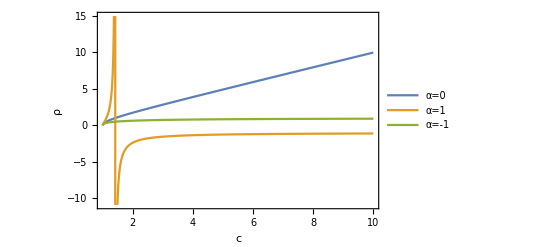

```mathematica
κ=1;
ρ[c]/.ρSolution/.C[1]-> {0,1,-1};
Plot[%,{c,1,10}, Frame->True, FrameLabel->{"c","ρ"},PlotLegends->Placed[{"α=0","α=1", "α=-1"},{Right, Bottom}]]
Clear[κ]
```

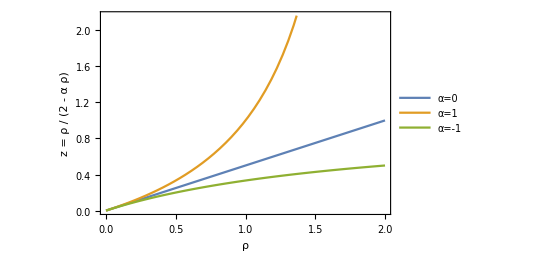

```mathematica
ρ/(2 - α ρ)/.α-> {0,1,-1};
Plot[%,{ρ,0,2}, Frame->True, FrameLabel->{ρ,"z = ρ / (2 - α ρ) " },PlotLegends->Placed[{"α=0","α=1", "α=-1"},{Left, Top}]]
```